# Flow Calibration Tests

For Calibration File generation, see flowTestData .091016.nb

```mathematica
<<NounouM`
```

<<KazukazuM version 0.5.20110118 loaded on: Tue 25 Jan 2011 20:33:26>>

<<NounouM version 0.5.20110119 loaded on: Tue 25 Jan 2011 20:33:27>>

```mathematica
cd=SetDirectory[NotebookDirectory[]]
```

V:\Documents\k.vsd\_figures\vsdMeth\flow field

```mathematica
Needs["ErrorBarPlots`"]
```

## Serialize Translation Speed

```mathematica
cd=SetDirectory[NotebookDirectory[]]
```

C:\Users\Kenta\Documents\k.vsd\_documents\_figures\vsdMeth\flow field

```mathematica
Save["translationSpeedResults.m",{translationSpeeds,translationAngles,translationNoise}]
```

```mathematica
Get["translationSpeedResults.m"];
```

## Test

```mathematica
ShowJavaConsole[]
```

«JavaObject[com.wolfram.jlink.ui.ConsoleWindow]»

```mathematica
tempdata=NNMDataNew[cd<>"\\testfiles\\translation_"<>ToString[10]<>"_"<>ToString[3.]<>"_"<>ToString[60]<>"_"<>ToString[0]<>".da"]
```

NNMData[«JavaObject[edu.georgetown.nnm.NNMDataSource]»]

```mathematica
tempflow=JavaNew[$NNJFlowClassPath,tempdata[[1]]]
```

«JavaObject[edu.georgetown.nnj.filterblocks.flow.NNJFlow]»

```mathematica
tempflow@setFlowRing[2]
```

```mathematica
tempflow@setMaxShift[5];tempflow@getMaxShift[]
```

5

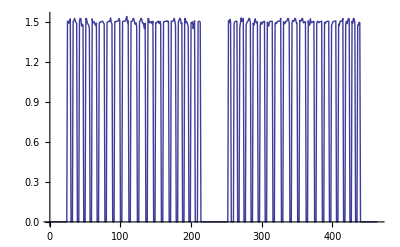

```mathematica
ListLinePlot[tempflow@getX[203],PlotRange->All]
```

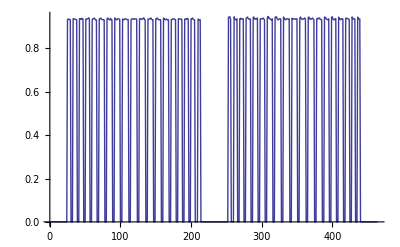

```mathematica
ListLinePlot[tempflow@getR[203],PlotRange->All]
```

```mathematica
Mean[Select[tempflow@getR[203],#>0.5&]]
```

0.936063

```mathematica
res2=tempflow@getResults[200]
```

```mathematica
Histogram[res1[[ All,2]] ]
```

```mathematica
tempflow=NNMFlowNew[tempdata,200]
```

NNMFlow[{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,{1.50034,2.51913,-0.0187306,0.0528662,0.935277},{1.50392,2.56283,-0.0378152,0.0528574,0.932587},{1.48589,2.60658,-0.018862,0.000212533,0.931151},{1.50386,2.60031,-0.0433168,0.105767,0.933496},{1.48214,2.60029,-0.0218499,3.25965×10^-6,0.931156},Null,Null,Null,{1.50392,2.56283,-0.0378152,0.0528574,0.932587},{1.50388,2.6003,-0.0379733,0.0000181287,0.931829},{1.50386,2.60032,-0.0815367,7.35128×10^-6,0.936207},{1.50755,2.56912,-0.043594,0.0530161,0.932752},{1.50025,2.59404,-0.022003,-0.0528738,0.931224},{1.50394,2.60033,0.0377894,-1.8128×10^-16,0.931828},Null,Null,Null,{1.50388,2.6003,-0.0379733,0.0000181287,0.931829},{1.50386,2.60032,-0.0815367,7.35128×10^-6,0.936207},{1.50749,2.56911,-0.0818015,-0.0528806,0.936898},{1.52562,2.56287,-0.0628294,-0.0528301,0.935326},{1.50752,2.60656,0.0377894,-0.10581,0.933351},{1.47513,2.5879,0.0430593,-0.0528899,0.932751},Null,Null,Null,{1.50386,2.60032,-0.0815367,7.35128×10^-6,0.936207},{1.50749,2.56911,-0.0818015,-0.0528806,0.936898},{1.5256,2.56286,-0.0628294,-0.0528804,0.935326},{1.52202,2.59407,0.0568712,-0.0000533099,0.93372},{1.48587,2.60658,0.0621929,-0.105884,0.935445},{1.49325,2.5817,0.0432601,-0.105757,0.933405},Null,Null,Null,{1.50749,2.56911,-0.0818015,-0.0528806,0.936898},{1.5256,2.56286,-0.0628294,-0.0528804,0.935326},{1.52204,2.59408,0.0568712,-5.44655×10^-6,0.93372},{1.49317,2.58163,0.0813048,7.35151×10^-6,0.936153},{1.50034,2.59413,0.062446,-0.0530366,0.934071},{1.48233,2.56291,0.0817936,-0.105725,0.938419},{1.46426,2.53166,0.000325859,0.0000145164,0.934143},Null,Null,Null,{1.5256,2.56286,-0.0628294,-0.0528804,0.935326},{1.52204,2.59408,0.0568712,-5.44655×10^-6,0.93372},{1.49317,2.58163,0.0813048,7.35151×10^-6,0.936153},{1.49318,2.58167,0.0815587,0.0000181295,0.936153},{1.50038,2.55667,0.100905,0.0000228229,0.940321},{1.44974,2.54411,0.000377981,-0.0529116,0.934398},{1.47141,2.58159,0.000388658,0.0528865,0.931365},{1.50744,2.60653,0.000272238,-2.26622×10^-16,0.930855},Null,Null,Null,{1.52204,2.59408,0.0568712,-5.44655×10^-6,0.93372},{1.49317,2.58163,0.0813048,7.35151×10^-6,0.936153},{1.49318,2.58167,0.0815587,0.0000181295,0.936153},{1.50038,2.55667,0.100905,0.0000228229,0.940321},{1.50034,2.51913,-0.0187306,0.0528662,0.935277},{1.50395,2.56284,-0.0378152,0.0529484,0.932587},{1.50392,2.60033,0.000272238,0.10595,0.931942},{1.51104,2.61278,-0.0215921,0.0528793,0.931845},Null,Null,Null,{1.49317,2.58163,0.0813048,7.35151×10^-6,0.936153},{1.49318,2.58167,0.0815587,0.0000181295,0.936153},{1.50038,2.55667,0.100905,0.0000228229,0.940321},{1.50034,2.51913,-0.0187306,0.0528662,0.935277},{1.50392,2.56283,-0.0378152,0.0528574,0.932587},{1.50394,2.60033,-0.0379733,0.000212533,0.931828},{1.51118,2.57538,-0.0624309,0.105944,0.935404},{1.49661,2.5878,-0.0218499,0.0528871,0.931185},Null,Null,Null,{1.49318,2.58167,0.0815587,0.0000181295,0.936153},{1.50038,2.55667,0.100905,0.0000228229,0.940321},{1.50034,2.51913,-0.0187306,0.0528662,0.935277},{1.50392,2.56283,-0.0378152,0.0528574,0.932587},{1.50388,2.6003,-0.0379733,0.0000181287,0.931829},{1.50386,2.60032,-0.0815367,7.35128×10^-6,0.936207},{1.48948,2.57539,-0.0627025,-0.0527551,0.93426},{1.51114,2.57534,-0.0437344,-0.0528738,0.932654},{1.522,2.59408,0.0377894,-0.0528847,0.932537},Null,Null,Null,{1.50034,2.51913,-0.0187306,0.0528662,0.935277},{1.50392,2.56283,-0.0378152,0.0528574,0.932587},{1.50388,2.6003,-0.0379733,0.0000181287,0.931829},{1.50386,2.60032,-0.0815367,7.35128×10^-6,0.936207},{1.50749,2.56911,-0.0818015,-0.0528806,0.936898},{1.5256,2.56286,-0.0628294,-0.0528804,0.935326},{1.50755,2.60657,0.0377593,-0.10581,0.93335},{1.49318,2.58165,0.0430593,-0.105771,0.933406},{1.48967,2.57547,0.0432601,-9.06591×10^-17,0.932201},Null,Null,Null,{1.50392,2.56283,-0.0378152,0.0528574,0.932587},{1.50388,2.6003,-0.0379733,0.0000181287,0.931829},{1.50386,2.60032,-0.0815367,7.35128×10^-6,0.936207},{1.50749,2.56911,-0.0818015,-0.0528806,0.936898},{1.5256,2.56286,-0.0628294,-0.0528804,0.935326},{1.52204,2.59408,0.0568712,-5.44655×10^-6,0.93372},{1.46782,2.61284,0.0813048,-0.105884,0.938786},{1.48235,2.6004,0.0432601,-0.158807,0.93536},{1.47518,2.55045,0.06006,-0.0528742,0.935542},Null,Null,Null,{1.50386,2.60032,-0.0815367,7.35128×10^-6,0.936207},{1.50749,2.56911,-0.0818015,-0.0528806,0.936898},{1.5256,2.56286,-0.0628294,-0.0528804,0.935326},{1.52204,2.59408,0.0568712,-5.44655×10^-6,0.93372},{1.49317,2.58163,0.0813048,7.35151×10^-6,0.936153},{1.48228,2.60038,0.0815587,-0.0530366,0.93674},{1.47502,2.58786,0.100904,-0.105876,0.941247},{1.4498,2.54415,0.000325859,-0.0528372,0.934397},Null,Null,Null,{1.5256,2.56286,-0.0628294,-0.0528804,0.935326},{1.52204,2.59408,0.0568712,-5.44655×10^-6,0.93372},{1.49317,2.58163,0.0813048,7.35151×10^-6,0.936153},{1.49318,2.58167,0.0815587,0.0000181295,0.936153},{1.50038,2.55667,0.100905,0.0000228229,0.940321},{1.48224,2.52538,0.000379157,0.0527902,0.934398},{1.4714,2.58158,0.000408267,0.0528865,0.931365},{1.48939,2.61278,0.000272238,0.0528841,0.931346},Null,Null,Null,{1.49317,2.58163,0.0813048,7.35151×10^-6,0.936153},{1.49318,2.58167,0.0815587,0.0000181295,0.936153},{1.50038,2.55667,0.100905,0.0000228229,0.940321},{1.50034,2.51913,-0.0187306,0.0528662,0.935277},{1.50392,2.56283,-0.0378152,0.0528574,0.932587},{1.50393,2.60034,0.000252626,0.10595,0.931942},{1.49298,2.61903,-0.0215921,0.105767,0.932956},{1.48214,2.60029,-0.0218499,-1.35954×10^-16,0.931156},Null,Null,Null,{1.50038,2.55667,0.100905,0.0000228229,0.940321},{1.50034,2.51913,-0.0187306,0.0528662,0.935277},{1.50392,2.56283,-0.0378152,0.0528574,0.932587},{1.50388,2.6003,-0.0379733,0.0000181287,0.931829},{1.52923,2.56913,-0.0815367,0.105944,0.938782},{1.49665,2.58783,-0.0218499,0.0530161,0.931185},{1.48218,2.6003,-0.022003,3.25962×10^-6,0.931155},Null,Null,Null,{1.50392,2.56283,-0.0378152,0.0528574,0.932587},{1.50388,2.6003,-0.0379733,0.0000181287,0.931829},{1.50386,2.60032,-0.0815367,7.35128×10^-6,0.936207},{1.50753,2.56914,-0.0818015,-0.0527551,0.936898},{1.52562,2.56287,-0.0628342,-0.0528301,0.935326},{1.50754,2.60658,0.0377894,-0.105764,0.93335},Null,Null,Null,{1.50386,2.60032,-0.0815367,7.35128×10^-6,0.936207},{1.50749,2.56911,-0.0818015,-0.0528806,0.936898},{1.5256,2.56286,-0.0628294,-0.0528804,0.935326},{1.54007,2.58782,0.0377643,-0.0000533099,0.933192},{1.49316,2.58164,0.0430894,-0.105771,0.933406},{1.50772,2.56921,0.0432601,-0.0528702,0.932751},Null,Null,Null,{1.5256,2.56286,-0.0628294,-0.0528804,0.935326},{1.52204,2.59408,0.0568712,-5.44655×10^-6,0.93372},{1.49317,2.58163,0.0813048,7.35151×10^-6,0.936153},{1.48229,2.60038,0.0433377,-0.158807,0.93536},{1.49323,2.54421,0.06006,-0.105725,0.93666},{1.46425,2.53166,0.000325859,4.53326×10^-17,0.934143},Null,Null,Null,Null,{1.49318,2.58167,0.0815587,0.0000181295,0.936153},{1.47502,2.58786,0.100905,-0.105876,0.941247},{1.4498,2.54415,0.000325859,-0.0528372,0.934397},{1.48945,2.57533,0.000388658,-2.26646×10^-16,0.930648},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,{1.48955,2.57538,-0.0818491,-3.25962×10^-6,0.936322},{1.50396,2.60034,0.0759834,0.105764,0.936899},{1.50032,2.59409,0.100408,0.0530563,0.93959},{1.49318,2.58167,0.0815587,0.0000181295,0.936153},Null,Null,Null,Null,{1.49321,2.58166,0.119577,0.105771,0.944983},{1.48588,2.60661,0.100666,0.105908,0.941078},{1.50036,2.55666,0.100905,0.0000980236,0.940321},{1.50034,2.51913,-0.0187306,0.0528662,0.935277},{1.50392,2.56283,-0.0378152,0.0528574,0.932587},Null,Null,Null,{1.47515,2.58793,0.119801,0.0528702,0.944224},{1.4859,2.56913,0.119995,0.105798,0.945582},{1.50037,2.51915,-0.0187306,0.0527778,0.935277},{1.50392,2.56283,-0.0378152,0.0528574,0.932587},{1.50388,2.6003,-0.0379733,0.0000181287,0.931829},{1.50386,2.60032,-0.0815367,7.35128×10^-6,0.936207},Null,Null,Null,{1.48233,2.56291,0.119995,3.62664×10^-16,0.944379},{1.47499,2.55035,-0.0595557,0.0528372,0.935544},{1.50395,2.56286,-0.076038,-0.053083,0.936391},{1.50388,2.6003,-0.0379733,0.0000181287,0.931829},{1.50386,2.60032,-0.0815367,7.35128×10^-6,0.936207},{1.50749,2.56911,-0.0818015,-0.0528806,0.936898},{1.5256,2.56286,-0.0628294,-0.0528804,0.935326},Null,Null,Null,{1.47852,2.59402,-0.0977709,-0.0000145153,0.939109},{1.50387,2.6003,-0.0761989,-0.105752,0.9369},{1.48585,2.6066,-0.100651,-0.000119887,0.939583},{1.50749,2.56911,-0.0818015,-0.0528806,0.936898},{1.5256,2.56286,-0.0628294,-0.0528804,0.935326},{1.52204,2.59408,0.0568712,-5.44655×10^-6,0.93372},{1.49317,2.58163,0.0813048,7.35151×10^-6,0.936153},Null,Null,Null,{1.50385,2.6003,-0.119785,-0.105767,0.944908},{1.48946,2.57537,-0.100911,-0.0529325,0.939881},{1.52559,2.56285,-0.0628294,-0.0528318,0.935326},{1.52204,2.59408,0.0568712,-5.44655×10^-6,0.93372},{1.49317,2.58163,0.0813048,7.35151×10^-6,0.936153},{1.49318,2.58167,0.0815587,0.0000181295,0.936153},{1.50038,2.55667,0.100905,0.0000228229,0.940321},Null,Null,Null,{1.49308,2.5816,-0.119981,-3.25965×10^-6,0.943367},{1.47507,2.58787,-0.0818491,0.052921,0.936897},{1.49668,2.62529,0.0568712,0.105877,0.935651},{1.49317,2.58163,0.0813048,7.35151×10^-6,0.936153},{1.49318,2.58167,0.0815587,0.0000181295,0.936153},{1.50038,2.55667,0.100905,0.0000228229,0.940321},{1.50034,2.51913,-0.0187306,0.0528662,0.935277},{1.50392,2.56283,-0.0378152,0.0528574,0.932587},Null,Null,Null,{1.48955,2.57538,-0.0818491,-1.8127×10^-16,0.936322},{1.51486,2.58164,0.0977304,0.105764,0.940552},{1.48227,2.60034,0.11952,0.158815,0.94727},{1.49318,2.58167,0.0815587,0.0000181295,0.936153},{1.50038,2.55667,0.100905,0.0000228229,0.940321},{1.50034,2.51913,-0.0187306,0.0528662,0.935277},{1.50392,2.56283,-0.0378152,0.0528574,0.932587},{1.50388,2.6003,-0.0379733,0.0000181287,0.931829},{1.50386,2.60032,-0.0815367,7.35128×10^-6,0.936207},Null,Null,Null,{1.50768,2.56918,0.119577,0.0528899,0.944224},{1.49319,2.58166,0.119779,0.105757,0.944984},{1.51842,2.55041,0.120015,0.0000980236,0.945382},{1.50034,2.51913,-0.0187306,0.0528662,0.935277},{1.50392,2.56283,-0.0378152,0.0528574,0.932587},{1.50388,2.6003,-0.0379733,0.0000181287,0.931829},{1.50386,2.60032,-0.0815367,7.35128×10^-6,0.936207},{1.50749,2.56911,-0.0818015,-0.0528806,0.936898},{1.5256,2.56286,-0.0628294,-0.0528804,0.935326},Null,Null,Null,{1.48592,2.56914,0.119995,0.105725,0.945581},{1.50037,2.51915,-0.0187294,0.0527778,0.935277},{1.50397,2.56285,-0.0378152,0.0526652,0.932587},{1.50388,2.6003,-0.0379733,0.0000181287,0.931829},{1.50386,2.60032,-0.0815367,7.35128×10^-6,0.936207},{1.50749,2.56911,-0.0818015,-0.0528806,0.936898},{1.5256,2.56286,-0.0628294,-0.0528804,0.935326},{1.52204,2.59408,0.0568712,-5.44655×10^-6,0.93372},Null,Null,Null,{1.45694,2.5566,-0.0595557,-0.0000145164,0.935807},{1.49305,2.58157,-0.0977709,-0.053083,0.939211},{1.52926,2.56911,-0.0379733,-0.105928,0.934189},{1.50386,2.60032,-0.0815367,7.35128×10^-6,0.936207},{1.50749,2.56911,-0.0818015,-0.0528806,0.936898},{1.5256,2.56286,-0.0628294,-0.0528804,0.935326},{1.52204,2.59408,0.0568712,-5.44655×10^-6,0.93372},{1.49317,2.58163,0.0813048,7.35151×10^-6,0.936153},{1.49318,2.58167,0.0815587,0.0000181295,0.936153},Null,Null,Null,{1.47852,2.59402,-0.0977709,-2.26646×10^-16,0.939109},{1.49298,2.61901,-0.0979216,-0.105752,0.940982},{1.50391,2.60034,-0.119757,-0.105898,0.944908},{1.50749,2.56911,-0.0818015,-0.0528806,0.936898},{1.5256,2.56286,-0.0628294,-0.0528804,0.935326},{1.52204,2.59408,0.0568712,-5.44655×10^-6,0.93372},{1.49317,2.58163,0.0813048,7.35151×10^-6,0.936153},{1.49318,2.58167,0.0815587,0.0000181295,0.936153},{1.50038,2.55667,0.100905,0.0000228229,0.940321},Null,Null,Null,{1.48938,2.61279,-0.119785,-0.0528793,0.944139},{1.47499,2.58785,-0.12001,-0.0528871,0.944225},{1.50754,2.56909,-0.0819295,-0.0528318,0.936898},{1.52204,2.59408,0.0568712,-5.44655×10^-6,0.93372},{1.49317,2.58163,0.0813048,7.35151×10^-6,0.936153},{1.49318,2.58167,0.0815587,0.0000181295,0.936153},{1.50038,2.55667,0.100905,0.0000228229,0.940321},{1.50034,2.51913,-0.0187306,0.0528662,0.935277},Null,Null,Null,{1.47509,2.58788,-0.0818491,0.0528738,0.936897},{1.49667,2.62529,0.0568761,0.105877,0.935651},{1.48227,2.60034,0.0813048,0.0530563,0.93674},{1.49318,2.58167,0.0815587,0.0000181295,0.936153},{1.50038,2.55667,0.100905,0.0000228229,0.940321},{1.50034,2.51913,-0.0187306,0.0528662,0.935277},{1.50392,2.56283,-0.0378152,0.0528574,0.932587},Null,Null,Null,{1.49679,2.58789,0.0977304,0.0528847,0.939116},{1.48231,2.60037,0.119577,0.158815,0.947269},{1.46782,2.61286,0.0815587,0.105908,0.938786},{1.50038,2.55667,0.100905,0.0000228229,0.940321},{1.50034,2.51913,-0.0187306,0.0528662,0.935277},{1.50392,2.56283,-0.0378152,0.0528574,0.932587},{1.50388,2.6003,-0.0379733,0.0000181287,0.931829},Null,Null,Null,{1.48962,2.57544,0.119577,-1.81298×10^-16,0.943592},{1.4932,2.58167,0.119801,0.105757,0.944984},{1.48592,2.56914,0.120017,0.105798,0.945581},{1.50034,2.51913,-0.0187306,0.0528662,0.935277},{1.50392,2.56283,-0.0378152,0.0528574,0.932587},{1.50388,2.6003,-0.0379733,0.0000181287,0.931829},{1.50386,2.60032,-0.0815367,7.35128×10^-6,0.936207},Null,Null,Null,{1.50038,2.55666,0.119995,0.0528742,0.944915},{1.48588,2.53163,-0.0378389,0.0528372,0.934937},{1.4859,2.5691,-0.0569261,0.0526652,0.933974},{1.50388,2.6003,-0.0379733,0.0000181287,0.931829},{1.50386,2.60032,-0.0815367,7.35128×10^-6,0.936207},{1.50749,2.56911,-0.0818015,-0.0528806,0.936898},Null,Null,Null,{1.49299,2.58154,-0.0977709,-0.0528865,0.939212},{1.51119,2.57537,-0.0570883,-0.105928,0.934872},{1.5039,2.60035,-0.0815367,-0.000119887,0.936206},{1.50749,2.56911,-0.0818015,-0.0528806,0.936898},{1.5256,2.56286,-0.0628294,-0.0528804,0.935326},Null,Null,Null,{1.49298,2.61901,-0.0979216,-0.105752,0.940982},{1.50391,2.60034,-0.119757,-0.105898,0.944908},{1.50751,2.56912,-0.0818015,-0.0529325,0.936898},{1.5256,2.56286,-0.0628294,-0.0528804,0.935326},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}]

```mathematica
tempdata=NNMDataNew[cd<>"\\testfiles\\translation_"<>ToString[10]<>"_"<>ToString[2.]<>"_"<>ToString[60]<>"_"<>ToString[10]<>".da"];
```

```mathematica
tempflow=NNMFlowNew[tempdata,200,FlowRing->1(*,MaxShift->16*),FlowReliabilityThreshold->0.1];
```

```mathematica
tempflow=DeleteCases[tempflow,(x_/;x==Null),2][[1]];
```

```mathematica
{Mean[tempflow[[All, 1]]],Mean[tempflow[[All, 2]]]}
```

{-5.48257,-10.4074}

```mathematica
Norm[%]
```

11.7632

```mathematica
{Mean[tempflow[[All, 3]]],Mean[tempflow[[All, 4]]],Mean[tempflow[[All, 5]]]}
```

{0.0352497,0.00839111,0.33321}

```mathematica
Sort[tempflow,(#1[[5]]>#2[[5]])&]
```

{{-5.66411,-9.81124,10.0018,9.54275,0.748263},{-17.3344,-12.6964,0.00338349,3.18371,0.706895},{-2.33032,-21.3619,-0.00286034,3.18917,0.706895},{-9.00351,-15.592,-6.66815,-6.36273,0.68826},{2.66623,-18.4776,-3.33982,0.000976054,0.668321},{-7.338,-12.6968,-9.99717,-6.37013,0.668321},{-15.6712,-9.81757,0.0017715,3.17556,0.66555},{-7.33561,-18.4743,-3.32599,6.36709,0.641021},{-7.32775,-18.4777,-6.67161,3.17784,0.641021},{-12.3442,-15.5896,6.66852,-3.181,0.641021},{-7.33197,-6.93515,6.67206,-9.54946,0.608969},{1.00174,-15.5861,-0.00312825,6.36302,0.598131},{0.998358,-15.5946,0.00212347,6.37069,0.598131},{-4.00106,-12.6991,3.3236,-9.54688,0.598131},{-3.99161,-12.7039,-10.0026,3.19825,0.59813},{-10.6664,-12.7,9.99991,-3.17961,0.59058},{-10.6689,-12.6957,9.99428,3.19333,0.59058},{-5.66497,-15.5817,-9.99315,-3.17137,0.59058},{-10.6612,-12.6976,-3.33264,6.36342,0.590384},{-5.6627,-15.5878,-3.33305,6.37597,0.590384},{-13.9965,-12.6936,3.33243,-3.18405,0.587607},{-13.999,-12.6962,3.33014,-3.1729,0.587607},{-13.9974,-12.6953,-3.34425,3.18913,0.587606},{4.33367,-15.5865,-3.33303,-3.18616,0.563979},{-8.99985,-15.5841,-6.66773,-0.00212719,0.559133},{-5.66904,-9.8168,-0.000962121,9.54648,0.557713},{-5.6659,-9.808,-9.99389,-0.00204129,0.557712},{-2.33773,-15.5873,3.33425,-3.17448,0.555445},{-4.00032,-18.4739,-3.33313,-6.37103,0.539517},{-4.00062,-18.4752,6.67159,3.1975,0.539517},{-7.33438,-18.4777,-3.3356,-0.00513152,0.53656},{-12.3264,-15.589,3.32578,0.00189259,0.53656},{-12.3375,-15.5848,-3.32628,-0.00994635,0.53656},{-12.339,-15.5921,-0.0148995,-3.18377,0.536559},{-10.6611,-12.7045,-6.65782,-6.3642,0.535761},{-5.66323,-15.5809,-6.66258,-6.35914,0.535761},{-10.674,-12.6951,-6.67512,6.35502,0.535761},{-14.002,-12.703,-0.00518614,0.0106572,0.53239},{-7.3328,-12.7012,0.00316397,9.54937,0.530935},{-10.6611,-6.922,-9.99331,-3.18343,0.529043},{-14.0018,-6.93315,3.33589,3.17825,0.524502},{2.66739,-12.7002,-6.66554,3.1838,0.521087},{-12.3331,-4.03617,6.6642,-3.18175,0.521087},{2.66361,-12.6971,6.66386,-3.18721,0.521087},{-12.3358,-4.03875,6.66995,3.17634,0.521087},{-8.99598,-15.5878,-3.33029,-3.1909,0.507096},{-12.3346,-9.81229,-3.33726,6.36805,0.502481},{-12.337,-9.81174,3.33818,-6.36407,0.502481},{-12.3388,-9.81634,3.3322,6.37068,0.502481},{-12.3322,-9.81051,3.32689,-6.36034,0.502481},{-12.3301,-9.80929,3.33518,-6.35877,0.502481},{-0.675256,-18.4754,0.00615103,0.00318843,0.486765},{-2.3321,-15.5941,-0.00412902,0.000580681,0.486673},{-2.33585,-15.5915,-0.00290252,-0.0158388,0.486672},{1.00146,-15.5968,3.33876,6.36092,0.479843},{-8.99631,-15.5896,6.66811,3.19159,0.474969},{-10.6684,-18.473,-0.00364161,-3.17685,0.474593},{-10.6722,-12.7049,3.32957,-0.00245472,0.471188},{-10.6707,-12.703,3.33829,-0.0123625,0.471188},{-0.670652,-12.7054,6.6689,6.36876,0.465986},{-10.6716,-6.92386,-6.6679,6.35945,0.465986},{-7.33312,-18.4721,-3.3322,3.19365,0.465782},{-4.00922,-18.4722,3.33749,0.00032703,0.45515},{-4.00765,-18.4802,0.00925073,3.18217,0.455149},{-10.6683,-12.7066,0.000684215,-6.37023,0.442055},{-10.6622,-12.6958,0.00385878,6.36274,0.442055},{-5.66292,-15.5806,0.00222088,-6.36306,0.442055},{-5.67973,-15.5892,-0.0000749724,-6.35533,0.442054},{-2.33408,-4.04235,-10.0026,4.04596×10^-7,0.440283},{-5.66315,-9.81505,3.33204,9.54651,0.4371},{-5.6667,-9.82013,3.33134,-9.55511,0.437099},{-5.67105,-9.81915,-3.32872,9.55228,0.437099},{-5.66157,-9.82272,-10.0028,-3.17556,0.437099},{-9.00222,-9.81063,-0.00488856,3.18083,0.433861},{-9.00276,-9.80654,-0.000681862,3.18744,0.433861},{-7.34064,-18.4718,-0.00191529,-0.00891735,0.431282},{-5.66615,-4.0474,3.33368,9.5513,0.427536},{-0.663651,-6.92367,-9.99489,-3.18171,0.427536},{-5.65817,-4.04169,-3.33109,9.54522,0.427535},{-0.666904,-6.93525,3.33835,-9.55479,0.427535},{-7.33089,-12.705,6.66304,-3.18258,0.425515},{-7.3334,-12.7034,6.67291,3.18304,0.425515},{-7.33437,-12.6967,6.6686,3.18784,0.425515},{-7.33552,-12.7003,-6.67033,-3.17644,0.425515},{-7.33684,-12.7035,-3.32626,6.3689,0.425515},{-7.33527,-12.6968,6.67436,3.18126,0.425515},{-7.3257,-12.7,-6.67323,-3.18072,0.425515},{-7.33551,-12.6982,6.66391,3.17225,0.425515},{-7.34305,-12.7024,3.34132,6.37014,0.425515},{-7.32551,-12.703,-6.67759,-3.17909,0.425515},{-7.34696,-12.7056,3.33345,-6.36804,0.425515},{-7.32005,-12.7053,-6.67399,3.19004,0.425514},{-2.33137,-9.82205,0.00338875,6.37022,0.410744},{-7.33408,-12.7086,6.66509,-6.36683,0.40493},{-7.33531,-12.6967,-6.67197,-6.37149,0.40493},{-7.32794,-12.6999,-6.66535,-6.3548,0.40493},{-4.00321,-12.6984,-0.000853067,6.36559,0.403932},{-4.00426,-12.702,0.00308171,6.36409,0.403932},{-8.99946,-9.8173,6.6683,0.00475723,0.403932},{-3.99718,-12.7006,-0.000176342,-6.37197,0.403932},{-4.00126,-12.6992,6.67572,-0.00180584,0.403932},{-3.99358,-12.6962,6.66726,-0.0068381,0.403932},{-9.00244,-9.821,-0.00799152,6.37448,0.403931},{-2.33285,-15.5913,3.33271,-0.00108634,0.402057},{-2.3324,-15.5913,0.00467654,3.18417,0.402057},{-2.32982,-15.5879,0.00342588,3.18636,0.402057},{-12.337,-9.81653,3.33203,-0.00577518,0.402057},{-12.3346,-9.8157,-3.32622,0.00137845,0.402057},{-2.32814,-15.5854,3.32752,-0.0025957,0.402057},{-12.3336,-9.81451,-3.33969,-0.00746608,0.402057},{-12.3261,-9.82072,-3.32802,-0.00131264,0.402057},{-12.329,-9.81369,-3.32712,0.00739156,0.402057},{-12.3275,-9.81348,0.00836022,-3.17711,0.402057},{-2.33229,-15.5845,-0.0115091,-3.17457,0.402057},{-12.3411,-9.81821,-3.34288,0.00885558,0.402057},{-12.3339,-9.82712,-0.000492224,3.19464,0.402056},{-10.6647,-12.7021,3.33088,3.18206,0.400671},{-5.66268,-15.5882,-3.33451,-3.17763,0.400671},{-5.66757,-15.5878,3.33178,-3.17645,0.400671},{-5.66844,-15.5934,3.33806,-3.1878,0.400671},{-5.66376,-15.5921,3.32946,-3.17297,0.400671},{-8.99753,-15.5872,0.00686698,3.18132,0.399604},{-9.00543,-15.5903,0.00109097,3.18892,0.399604},{-8.99499,-15.5895,3.34317,0.00548406,0.399604},{-8.99509,-15.5887,0.0059961,3.17307,0.399604},{-9.01237,-15.5894,-3.34067,0.00931422,0.399604},{-7.33,-12.7004,0.00405238,-0.000309179,0.398071},{2.66505,-6.93,-3.33095,6.36694,0.386861},{-2.32942,-15.5879,6.67532,-0.0166953,0.385414},{1.00411,-15.5852,-0.00421521,-3.18731,0.384542},{-13.999,-6.93474,-3.32873,0.00191906,0.384542},{-12.3283,-4.04342,3.34022,0.000352198,0.381726},{2.66885,-12.7025,-0.00327057,3.19253,0.381725},{0.997164,-9.81288,0.00176581,-6.36697,0.379229},{-0.668639,-6.9325,6.66729,-3.18592,0.375},{-0.66208,-6.92411,-3.33023,6.36708,0.375},{-5.6618,-4.03765,3.33101,6.36189,0.375},{-0.667553,-12.7011,-3.33758,-0.00263167,0.374511},{-10.6675,-6.92232,0.00236544,-3.17945,0.374511},{-10.6646,-6.93054,-0.00351591,-3.19109,0.374511},{-0.674764,-12.6996,-3.3348,-0.00698421,0.374511},{-2.33786,-9.82148,3.33443,9.55507,0.36421},{-5.66338,-15.5891,0.000702548,0.00357455,0.361965},{-5.66145,-15.5903,0.00357892,-0.00555996,0.361965},{-5.67089,-15.588,-0.00581818,-0.00589957,0.361965},{-5.67358,-15.5899,-0.00857575,-0.00426987,0.361965},{-9.00105,-15.5858,-3.3418,3.18222,0.356692},{-4.00171,-12.7034,-3.33871,3.18588,0.352006},{-9.0026,-9.81501,-3.33508,-3.17739,0.352006},{-3.99683,-12.7095,3.3408,3.18396,0.352005},{-3.99809,-12.6938,-3.34053,-3.17593,0.352005},{-4.00613,-12.7137,3.33466,-3.18605,0.352005},{-2.33169,-15.5902,-3.33138,-3.18453,0.348134},{-12.3342,-9.80853,3.333,-3.18305,0.348134},{-12.3292,-9.81523,3.32844,-3.17702,0.348134},{-2.33706,-15.5947,-3.33974,-3.18512,0.348134},{-12.3325,-9.80513,3.3321,3.17711,0.348134},{-4.00021,-12.7,3.33355,-6.36822,0.342048},{-8.9991,-9.81451,6.67097,-3.18315,0.342048},{-9.0035,-9.8166,-3.33076,6.36639,0.342048},{-3.99701,-12.7012,3.32988,6.36408,0.342048},{-9.00219,-9.81894,-6.66328,3.18474,0.342048},{-3.999,-12.7014,3.32707,6.3623,0.342048},{-9.001,-9.82085,-3.33173,6.37184,0.342048},{-8.99699,-9.80673,-6.6638,-3.1803,0.342048},{-3.99037,-12.7089,3.33478,-6.36862,0.342048},{-8.99395,-9.80968,6.6643,-3.17426,0.342048},{-7.33144,-12.7037,-0.000459322,3.18306,0.336642},{-7.33531,-12.6993,3.33539,0.000904355,0.336642},{-7.33704,-12.7003,3.33183,0.000241013,0.336642},{-7.33564,-12.6978,-3.33173,0.000405698,0.336642},{-7.33473,-12.709,0.00237005,-3.18291,0.336642},{-7.33104,-12.6962,0.00439039,3.1803,0.336642},{-7.34513,-12.7013,0.000359029,-3.18115,0.336642},{-7.32737,-12.7008,-0.0000330248,-3.19457,0.336642},{-7.33894,-12.6915,3.34417,-0.00256009,0.336641},{-2.32846,-9.8096,3.33606,3.18426,0.331847},{-4.00007,-6.92814,10.0005,-0.000535561,0.33035},{-7.32876,-12.7067,0.00543859,-6.3608,0.330271},{-7.33467,-12.7091,6.67276,0.0071076,0.330271},{-5.66712,-9.81206,0.00464135,9.546,0.327238},{-7.33007,-6.92786,-6.66992,-3.18357,0.322714},{-7.3284,-6.92733,-6.66655,3.18344,0.322714},{-7.33308,-6.92673,3.34003,-6.36481,0.322714},{-2.33739,-9.81067,-3.32862,-6.3641,0.322714},{-2.3308,-9.82201,6.671,-3.18845,0.322714},{-7.33978,-6.93125,6.67171,3.18849,0.322714},{-2.32802,-9.8132,-3.3233,6.36884,0.322714},{-7.32979,-6.91968,3.33721,6.36002,0.322714},{-2.34063,-9.81088,-6.67481,3.17596,0.322714},{-5.66248,-15.5864,3.33307,-0.00005609,0.321298},{-5.67155,-15.5872,-3.33535,0.00207482,0.321298},{-5.66617,-15.587,-0.00080134,-3.17546,0.321298},{-5.6685,-15.5949,-3.32652,0.00032947,0.321298},{-5.65537,-15.5859,3.33826,-0.00170434,0.321298},{-10.6661,-12.6976,3.32953,-0.0124537,0.321298},{-5.68033,-15.5931,0.00366184,-3.18175,0.321298},{-3.99679,-1.15323,-6.661,0.0000667973,0.311897},{-0.668447,-12.7008,-3.33328,-3.18486,0.310591},{-10.6665,-6.92421,3.33898,-3.18103,0.310591},{-10.6703,-6.93303,-3.33938,-3.18331,0.310591},{-10.6651,-6.91956,-3.33487,-3.18299,0.310591},{-0.665884,-12.7066,3.32555,3.18642,0.310591},{-0.660658,-12.6995,3.32771,-3.17641,0.31059},{-0.667156,-12.7017,3.33394,-3.19426,0.31059},{-9.00135,-4.0431,3.33452,-3.18447,0.305957},{1.00077,-9.81016,3.33138,-3.18113,0.305957},{-9.00348,-4.0451,-3.33697,-3.18656,0.305957},{-8.99494,-9.82056,-0.00957851,0.00108361,0.303942},{1.00129,-9.81168,-3.33251,-6.36282,0.303007},{0.99576,-9.81765,6.6662,-3.18502,0.303007},{-8.99843,-4.04298,-3.33793,-6.36378,0.303007},{-9.00411,-4.04125,6.66688,3.17902,0.303007},{0.994193,-9.81567,-3.33261,-6.36975,0.303007},{0.994067,-9.81794,6.67339,-3.18987,0.303006},{-7.32786,-12.7019,3.33592,3.18441,0.295904},{-7.32823,-12.701,-3.32877,3.17901,0.295904},{-7.33754,-12.7036,-3.34214,-3.18563,0.295904},{-7.33668,-12.7038,-3.34375,-3.18563,0.295904},{-7.34508,-12.6982,3.3434,3.17607,0.295904},{-5.6636,-9.81525,0.000342493,6.363,0.287981},{-5.66088,-9.8171,-6.66544,-0.000759607,0.287981},{-5.66836,-9.8099,-0.00368384,-6.36821,0.287981},{-5.67104,-9.8099,-6.66518,0.00125131,0.287981},{-5.6625,-9.81981,0.00171487,6.36959,0.287981},{-5.67426,-9.81454,-6.6709,0.00119829,0.287981},{-5.6738,-9.81161,6.66153,0.00451636,0.287981},{-5.66286,-9.81474,3.33087,-0.00377455,0.286833},{-5.67071,-9.81364,0.0048662,-3.18376,0.286833},{-5.66038,-9.81336,0.00385636,3.18377,0.286833},{-5.67052,-9.81142,3.32364,0.0000985894,0.286833},{-5.66611,-9.82025,3.32852,-0.00799347,0.286833},{2.66894,-12.7049,0.00675583,-0.00813741,0.272946},{-3.99727,-6.92483,-0.000212249,6.36262,0.272082},{-4.00134,-6.92223,-6.66529,0.00097274,0.272082},{-3.99852,-6.92565,0.00410347,-6.3623,0.272082},{-3.99732,-6.93741,-0.00192369,-6.36919,0.272081},{-3.98969,-12.7028,-0.00212672,6.35907,0.268302},{-5.66733,1.73175,3.33116,-3.18278,0.266764},{-0.664254,-12.697,0.000508004,-0.00231116,0.266068},{-0.670131,-12.7013,0.00582011,-0.000127092,0.266068},{-10.6617,-6.92525,0.000126021,0.0102325,0.266067},{-8.99854,-9.81395,3.33257,0.00287083,0.264388},{-3.99703,-12.7006,3.32925,0.00125477,0.264388},{-3.99876,-12.6978,3.33659,-0.00279809,0.264388},{-8.99818,-9.82008,0.00295823,-3.18856,0.264388},{-3.9923,-12.7071,3.33024,0.00233598,0.264387},{-3.99533,-12.7049,-0.00924859,3.18614,0.264387},{-9.00743,-9.81754,-3.34166,-0.000608595,0.264387},{-3.99645,-12.698,0.00304369,-3.19267,0.264387},{-4.0083,-12.7038,-3.33907,0.0067946,0.264387},{-4.00838,-12.695,0.0172992,3.18252,0.264387},{-7.33531,-12.6957,0.000418771,-0.00217469,0.263138},{-7.33004,-12.7002,0.00272828,-0.00641967,0.263138},{-7.33845,-12.6991,-0.00572189,0.0109847,0.263138},{-2.33455,-9.81282,0.00336507,-0.00567032,0.261329},{-5.66353,-9.81615,3.31985,-6.36744,0.252266},{-2.33451,-4.04117,3.3348,-6.3646,0.249061},{-5.66607,-9.81517,-3.33471,3.17836,0.24479},{-5.66123,-9.81342,3.32879,3.18247,0.24479},{-5.66461,-9.81616,3.33247,-3.19387,0.24479},{-5.67416,-9.81818,3.341,3.18668,0.24479},{-5.66183,-9.81601,-3.3323,3.19713,0.24479},{-5.65998,-9.82455,-3.32665,-3.19174,0.244789},{-7.33376,-12.7041,-0.00638565,-3.1889,0.239085},{-7.33263,-12.7017,0.00288348,-3.16797,0.239085},{-3.99329,-12.6987,3.33255,3.17534,0.237152},{-9.00299,-9.81048,-3.32435,-3.17968,0.237152},{-4.00618,-12.702,-3.33047,-3.19261,0.237152},{-4.00439,-12.7017,3.33041,-3.16703,0.237152},{4.3336,-9.81437,3.33137,0.00697657,0.235281},{-10.6685,-6.92194,3.32919,0.000293702,0.23467},{-0.669782,-12.6989,0.00665657,3.18146,0.23467},{-0.674897,-12.6979,3.32591,-0.000403854,0.23467},{-2.33328,-9.81652,-6.66635,-0.000420078,0.231367},{-7.33609,-6.92581,6.66636,-0.00207132,0.231367},{-2.32876,-9.81785,-0.0016907,-6.37238,0.231367},{2.66992,-6.93301,-6.66765,-0.000814085,0.230594},{-7.33056,-1.15676,-6.66673,-0.00602354,0.230594},{2.67022,-6.93122,6.67236,-0.00171593,0.230594},{-3.9967,-6.92773,3.33412,6.36733,0.226755},{-4.00206,-6.93173,3.33845,-6.36733,0.226755},{-4.00483,-6.92529,-6.66404,-3.18582,0.226755},{-4.00542,-6.9252,-3.33495,-6.37204,0.226755},{-4.00225,-6.93384,6.67288,-3.17931,0.226755},{-4.00337,-6.92097,-3.33641,6.35854,0.226755},{-3.99663,-6.91971,3.33525,-6.35797,0.226755},{-3.99209,-1.16111,3.32855,6.37297,0.222912},{-0.668989,-6.93046,-6.66756,-0.000721018,0.219863},{-0.669171,-6.92571,0.00335542,6.36788,0.219863},{-0.674329,-6.92854,-6.66947,-0.000804279,0.219863},{-5.66687,-4.03916,6.66763,-0.00972119,0.219862},{-2.33376,-9.81565,-3.3321,0.00128137,0.217938},{-2.33326,-9.81789,3.33256,-0.0020781,0.217938},{-2.3316,-9.81375,3.33209,-0.00295682,0.217938},{-7.32941,-6.92779,-3.33265,-0.00046236,0.217938},{-2.33624,-9.81112,3.33355,-0.00308942,0.217938},{-7.34088,-6.92695,3.33279,-0.00325819,0.217938},{-2.33247,-9.81427,-0.000820275,3.17484,0.217938},{-2.33016,-9.81479,-3.3329,0.00841512,0.217938},{-2.34174,-9.81649,-0.00501311,-3.18516,0.217938},{-7.33712,-6.92587,-3.33153,-0.00970652,0.217938},{-2.33183,-9.81877,-0.00221504,-3.19297,0.217938},{-2.32712,-9.81481,3.32922,0.00908238,0.217938},{-2.33587,-9.8233,-3.33671,-0.0120845,0.217938},{-3.99886,-6.93025,-3.33182,3.18252,0.208669},{-3.99518,-6.92932,3.33408,-3.18324,0.208669},{-4.0057,-6.92654,3.3326,-3.18189,0.208669},{-3.99501,-6.9256,3.32956,3.18207,0.208669},{-4.00018,-6.9207,-3.32981,3.1796,0.208669},{-4.00809,-6.9296,3.324,3.18551,0.208669},{-7.33582,-1.15799,0.000825776,-3.18169,0.20844},{-7.33423,-1.152,0.0066083,3.17747,0.20844},{2.6658,-6.93224,3.3423,0.000187282,0.20844},{-5.66582,-9.81055,0.0033259,-0.00182291,0.203939},{-5.67007,-9.80691,-0.000741964,-0.0068583,0.203938},{-9.00168,-4.03797,0.00185151,3.18382,0.202958},{-8.99911,-4.04072,-0.00436151,-3.18493,0.202958},{0.997319,-9.81176,-0.000294239,3.18762,0.202958},{1.00154,-9.81707,-0.00528989,3.18038,0.202958},{1.00112,-9.81117,0.00596044,3.182,0.202958},{1.00054,-9.81687,-0.00824595,-3.181,0.202957},{0.998776,-9.81115,-3.33336,0.00895293,0.202957},{0.997999,-9.81937,-3.33552,0.00941656,0.202957},{-9.00344,-4.03386,-0.00515895,-3.16961,0.202957},{-5.66469,-4.04249,-3.33479,0.00144795,0.193128},{-0.663987,-6.93046,-3.33226,-0.00330238,0.193128},{-5.66501,-4.042,3.3336,-0.00610744,0.193128},{-0.659506,-6.92883,-0.0108083,-3.18077,0.193128},{-2.33009,-9.81371,-3.33495,3.18409,0.191925},{-2.33377,-9.81749,-3.33552,3.18701,0.191925},{-7.33698,-6.92855,3.34151,3.18261,0.191925},{-7.33842,-6.92789,-3.32989,3.17453,0.191925},{-2.34409,-9.81294,3.33349,-3.18208,0.191925},{-2.32335,-9.81659,3.33079,3.17948,0.191925},{-7.34208,-6.93372,3.33607,-3.17853,0.191925},{-7.33181,-6.92949,-3.32437,-3.19055,0.191925},{-2.34307,-9.81238,3.33953,3.19158,0.191925},{-5.66733,-4.04124,-6.66707,-3.18097,0.188893},{-4.00047,-1.15378,-3.33275,-3.18267,0.185826},{-3.99826,-1.15237,-3.33011,3.18157,0.185826},{-5.66419,-9.81708,-3.33453,0.00232237,0.184156},{-5.66936,-9.81445,-3.3356,-0.00471389,0.184156},{-5.6676,-9.82057,0.00103367,-3.1908,0.184156},{-5.67768,-9.81451,3.33036,0.0101134,0.184155},{1.00662,-9.81855,-3.3352,-3.17461,0.180518},{-8.99707,-4.04949,3.34521,3.18793,0.180518},{2.66351,-6.92854,-3.33293,-3.18078,0.173525},{-3.9937,-6.93632,0.000686995,6.36885,0.1621},{-0.663843,-6.92512,3.3331,3.17952,0.161998},{-0.665791,-6.92861,3.32784,3.18534,0.161998},{-5.66025,-4.04511,-3.33447,-3.17832,0.161998},{-0.663993,-6.93402,-3.3398,3.18226,0.161998},{-2.33402,-9.82337,0.0000616981,0.0012808,0.15432},{-2.33047,-9.82005,0.00500016,0.00583629,0.15432},{-2.34202,-9.81407,-0.00117455,-0.00595324,0.15432},{-7.33484,-6.92608,0.00217251,0.0118909,0.15432},{1.00047,-9.81471,-0.000495146,-0.00275995,0.144079},{-7.33071,-6.93506,0.000311252,-3.18527,0.143406},{-5.66747,-9.82268,0.00518526,0.00464268,0.142901},{-3.99978,-6.93133,-6.15481×10^-6,-3.18629,0.135486},{-4.00002,-6.92845,-0.00209831,3.17857,0.135486},{-3.99419,-6.92539,-0.00086887,3.18138,0.135486},{-4.00572,-6.92711,-3.33386,0.00423507,0.135486},{-4.00181,-6.93305,-3.32527,-0.00192822,0.135486},{-3.99692,-6.93652,0.00484545,3.18246,0.135486},{-4.0001,-6.91898,-0.00274242,-3.17854,0.135486},{-3.99393,-6.91951,0.0136416,-3.18018,0.135486},{-7.32449,-1.15811,-0.00750126,-0.0101948,0.12015},{-0.663164,-6.9271,0.00122756,0.000832678,0.107879},{-0.669375,-6.93005,0.00207056,-0.0017103,0.107879},{-0.661881,-6.92843,-0.000461375,-0.000845727,0.107879},{-0.662931,-6.92835,-0.00386428,-0.00223812,0.107879},{-0.674406,-6.92622,-0.00360786,-0.00241419,0.107879},{-5.66678,-4.04857,0.00319056,-0.00780136,0.107879},{-0.667857,-6.92803,0.00228935,-3.18331,0.103287},{-5.66343,-4.04174,-0.00306513,-3.18264,0.103287},{-0.663825,-6.92256,-3.33715,0.00534918,0.103287},{-5.65947,-4.04153,-3.33815,-0.00435705,0.103287},{-5.66939,-4.04301,3.34013,-0.008798,0.103287}}

## Translation Speed

```mathematica
Options[NNMFlowNew]
```

{FudgeDetectors→{},ReturnJavaObject→False,FlowRing→3,MaxShift→20,FlowReliabilityThreshold→0.5,CorrelationWindowLength→80,InvertOptical→False,InvertNonOptical→False,TemporalFilter→None,TemporalFilterOrder→1600,DataWindow→{-1,-1},SpatialFilter→False,ExtractStimulusTimings→{}}

```mathematica
analyzeTranslation[detDiameterPer2Pi_,framesPerDetDiameter_, angle_, noisePercent_]:=
Module[{tempdata, tempflow,tempspeeds},
JavaBlock[
tempdata=NNMDataNew[cd<>"\\testfiles\\translation_"<>ToString[detDiameterPer2Pi]<>"_"<>ToString[framesPerDetDiameter]<>"_"<>ToString[angle]<>"_"<>ToString[noisePercent]<>".da"];
tempflow=NNMFlowNew[tempdata,RandomInteger[{120,280}],FlowRing->3,MaxShift->40,CorrelationWindowLength->140,FlowReliabilityThreshold->0.5][[1]];
Table[
tempflow=Join[tempflow,NNMFlowNew[tempdata,RandomInteger[{120,280}],FlowRing->3,MaxShift->40,CorrelationWindowLength->140,FlowReliabilityThreshold->0.75][[1]]],
{50}];
tempflow=DeleteCases[tempflow, x_/;(x===Null || x[[5]]==0.)];
tempspeeds= Norm[{#[[1]], #[[2]]}]& /@ tempflow;
{Mean[tempspeeds], StandardDeviation[tempspeeds], Mean[tempflow[[ All, 5 ]]]}
]]
```

```mathematica
translationSpeeds=Join[{#},analyzeTranslation[30,#,60,0]]& /@ 
Range[0.5,5.0,0.5];
```

```mathematica
translationSpeeds
```

{{0.5,0.463448,0.0252805,0.737475},{1.,0.883843,0.035919,0.817214},{1.5,1.504,0.0194552,0.912496},{2.,2.,0.,1.},{2.5,2.46155,0.0212644,0.948814},{3.,2.92181,0.0619795,0.94255},{3.5,3.5091,0.0217571,0.962599},{4.,4.,0.,1.},{4.5,4.47158,0.0279167,0.971495},{5.,5.47796,1.21072,0.875182}}

```mathematica
translationSpeeds=DeleteCases[translationSpeeds,x_/;(!NumberQ[x[[2]]])];
```

```mathematica
translationSpeeds=Drop[translationSpeeds, -1]
```

{{0.5,0.463448,0.0252805,0.737475},{1.,0.883843,0.035919,0.817214},{1.5,1.504,0.0194552,0.912496},{2.,2.,0.,1.},{2.5,2.46155,0.0212644,0.948814},{3.,2.92181,0.0619795,0.94255},{3.5,3.5091,0.0217571,0.962599},{4.,4.,0.,1.},{4.5,4.47158,0.0279167,0.971495}}

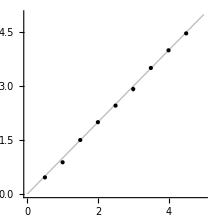

```mathematica
grTs=
Show[
ErrorListPlot[
Transpose[
{translationSpeeds[[All,{1,2}]],(ErrorBar /@ translationSpeeds[[All, 3]])}
],PlotRange->All,PlotStyle->Black,LabelStyle->(FontFamily->"Helvetica"),AspectRatio->1,ImageSize->72*3],
Plot[x,{x,0,5.0},PlotStyle->Directive[Thick,Opacity[0.25,Black]]]
]
```

```mathematica
Export["translationSpeeds.pdf",grTs]
```

translationSpeeds.pdf

### Test

```mathematica
data=NNMDataNew[cd <> "\\translation_20_2.5_60_10.da"];
```

```mathematica
flow=NNMFlowNew[data,200];
```

```mathematica
Histogram[flow[[1, All, 5]]]//Rasterize
```

-Graphics-

```mathematica
Options[NNMFlowPlot]
```

{Arrow→False,FlowScale→Automatic,FlowThreshold→∞,FlowReliabilityThreshold→0.8,FlowColor→(Opacity[#1,Black]&),PlotReciprocal→False,Prolog→{},GraphicsOptions→{PlotRange→{{-510.,490.},{-445.692,440.333}}}}

```mathematica
NNMFlowPlot[flow,FlowReliabilityThreshold->0.1, Arrow->True]//Rasterize
```

-Graphics-

```mathematica
ListLinePlot[data@readDataTraceAbsolute[#]& /@ Range[0,463, 70 ] ,PlotRange->{ {0,20},All}]//Rasterize
```

-Graphics-

## Serialize Translation Speed (Flow Rings)

```mathematica
cd=SetDirectory[NotebookDirectory[]]
```

Z:\My Documents\k.vsd\_documents\_figures\vsdMeth\flow field

```mathematica
Save["translationSpeedFRResults.m",{translationSpeeds1,translationSpeeds2,translationSpeeds3,translationSpeeds4}]
```

```mathematica
Get["translationSpeedFRResults.m"];
```

## Translation Speed (Flow Rings)

```mathematica
analyzeTranslationRings[detDiameterPer2Pi_,framesPerDetDiameter_, angle_, noisePercent_,ring_]:=
Module[{tempdata, tempflow,tempspeeds,tempflowObj},
JavaBlock[
tempdata=NNMDataNew[cd<>"\\testfiles\\translation_"<>ToString[detDiameterPer2Pi]<>"_"<>ToString[framesPerDetDiameter]<>"_"<>ToString[angle]<>"_"<>ToString[noisePercent]<>".da"];
tempflowObj=JavaNew[$NNJFlowClassPath,tempdata[[1]]];
tempflowObj@setFlowRing[ring];
tempflow=(tempflowObj@getResults[#])& /@ Range[50-1,350-1];
tempflow=NNMFlowNew[tempdata,RandomInteger[{100,300}]][[1]];
tempflow=DeleteCases[tempflow, x_/;x[[5]]==0.];
tempspeeds= Norm[{#[[1]], #[[2]]}]& /@ tempflow;
{Mean[tempspeeds], StandardDeviation[tempspeeds]}
]]
```

```mathematica
translationSpeeds1=Join[{#},analyzeTranslationRings[10,#,60,0,1]]& /@ 
Join[Range[0.01, 0.3, 0.01],Range[0.35, 0.45, 0.05],Range[0.5,5.0,0.5]]
```

{{0.01,0.,0.},{0.02,0.,0.},{0.03,0.300012,3.73388×10^-6},{0.04,0.118609,0.0327042},{0.05,0.,0.},{0.06,0.300052,0.00012397},{0.07,0.233333,0.0000558251},{0.08,0.4,4.16117×10^-6},{0.09,0.903436,0.00243941},{0.1,0.,0.},{0.11,1.10086,0.000548171},{0.12,0.599381,0.000199563},{0.13,0.43336,0.000017637},{0.14,0.349932,0.0000265602},{0.15,0.299995,0.000129607},{0.16,0.266667,3.57132×10^-6},{0.17,0.242855,0.0000171134},{0.18,0.225,0.000191449},{0.19,0.211039,0.000139806},{0.2,0.118609,0.0327042},{0.21,0.210007,0.0000413255},{0.22,0.220002,0.0000474173},{0.23,0.229866,0.000141971},{0.24,0.240084,0.0000671356},{0.25,0.249999,0.0000894013},{0.26,0.259915,0.0000960294},{0.27,0.270023,9.15075×10^-6},{0.28,0.279884,0.0000250296},{0.29,0.290005,0.0000725256},{0.3,0.300012,4.76995×10^-6},{0.35,0.349977,0.0000226798},{0.4,0.4,4.16117×10^-6},{0.45,0.449909,0.000179415},{0.5,0.499743,0.000284056},{1.,0.999979,0.0000668175},{1.5,1.50107,0.000265452},{2.,2.00065,0.000537373},{2.5,2.50195,0.00178694},{3.,3.00551,0.00415658},{3.5,3.45549,0.0208961},{4.,4.00944,0.0191778},{4.5,4.4988,0.0126194},{5.,4.98789,0.00924746}}

```mathematica
translationSpeeds2=Join[{#},analyzeTranslationRings[10,#,60,0,2]]& /@ 
Join[Range[0.01, 0.3, 0.01],Range[0.35, 0.45, 0.05],Range[0.5,5.0,0.5]]
```

{{0.01,0.,0.},{0.02,0.,0.},{0.03,0.299996,0.0000148827},{0.04,0.124732,0.0346325},{0.05,0.,0.},{0.06,0.300064,0.0000182536},{0.07,0.233173,0.0000725736},{0.08,0.4,4.16117×10^-6},{0.09,0.900073,0.000557636},{0.1,0.,0.},{0.11,1.10007,0.0000996888},{0.12,0.60021,0.000210042},{0.13,0.43341,0.000113601},{0.14,0.350027,0.0000225566},{0.15,0.299982,0.0000377759},{0.16,0.266667,3.57132×10^-6},{0.17,0.242857,0.000195611},{0.18,0.225115,0.0000652426},{0.19,0.211121,0.0000377832},{0.2,0.124732,0.0346325},{0.21,0.210006,0.00014748},{0.22,0.219529,0.000417639},{0.23,0.229999,7.91776×10^-6},{0.24,0.23999,5.27478×10^-6},{0.25,0.250005,0.000143466},{0.26,0.26,0.0000597546},{0.27,0.269903,0.0000214416},{0.28,0.280001,0.0000637923},{0.29,0.289995,0.0000494306},{0.3,0.300057,0.000181545},{0.35,0.349999,0.000084474},{0.4,0.4,4.16117×10^-6},{0.45,0.450061,0.0000383677},{0.5,0.500003,0.0000136848},{1.,0.999606,0.000175868},{1.5,1.49993,0.000440721},{2.,2.00151,0.00459116},{2.5,2.4898,0.00235057},{3.,3.00153,0.00390065},{3.5,3.50484,0.0030338},{4.,3.99975,0.00553054},{4.5,4.47847,0.0142198},{5.,5.00664,0.0174822}}

```mathematica
translationSpeeds3=Join[{#},analyzeTranslationRings[10,#,60,0,3]]& /@ 
Join[Range[0.01, 0.3, 0.01],Range[0.35, 0.45, 0.05],Range[0.5,5.0,0.5]]
```

{{0.01,0.,0.},{0.02,0.,0.},{0.03,0.300023,0.0000724142},{0.04,0.124732,0.0346325},{0.05,0.,0.},{0.06,0.300002,7.21642×10^-6},{0.07,0.233332,0.0000223114},{0.08,0.4,4.16117×10^-6},{0.09,0.898791,0.000665515},{0.1,0.,0.},{0.11,1.1025,0.00166644},{0.12,0.599318,0.000669479},{0.13,0.433336,6.79458×10^-6},{0.14,0.349958,0.0000176481},{0.15,0.300539,0.000112604},{0.16,0.266667,4.02524×10^-6},{0.17,0.241822,0.000236081},{0.18,0.224731,0.000215983},{0.19,0.21111,0.000107037},{0.2,0.124732,0.0346325},{0.21,0.210003,0.0000461461},{0.22,0.220001,0.000117704},{0.23,0.230003,0.0000353164},{0.24,0.240713,0.000234214},{0.25,0.25,5.23556×10^-6},{0.26,0.259889,0.0000275797},{0.27,0.269752,0.0000621623},{0.28,0.280004,0.0000465288},{0.29,0.290014,0.0000268002},{0.3,0.300008,0.0000222092},{0.35,0.349873,0.000117862},{0.4,0.4,4.16117×10^-6},{0.45,0.449852,0.00011148},{0.5,0.500224,0.0000824367},{1.,0.999507,0.000448131},{1.5,1.49963,0.000289945},{2.,1.9945,0.0063378},{2.5,2.50086,0.001845},{3.,3.00989,0.00488853},{3.5,3.52581,0.0117255},{4.,4.00234,0.0099348},{4.5,4.62773,0.0282831},{5.,4.97957,0.00980656}}

```mathematica
translationSpeeds4=Join[{#},analyzeTranslationRings[10,#,60,0,4]]& /@ 
Join[Range[0.01, 0.3, 0.01],Range[0.35, 0.45, 0.05],Range[0.5,5.0,0.5]]
```

{{0.01,0.,0.},{0.02,0.,0.},{0.03,0.300012,3.73388×10^-6},{0.04,0.124732,0.0346325},{0.05,0.,0.},{0.06,0.300039,0.0000919703},{0.07,0.23333,0.00009284},{0.08,0.4,4.16117×10^-6},{0.09,0.900622,0.00106844},{0.1,0.,0.},{0.11,1.10013,0.0000770511},{0.12,0.600972,0.000311339},{0.13,0.433327,0.0000161266},{0.14,0.350148,0.0000546859},{0.15,0.299642,0.0000730134},{0.16,0.266667,3.48425×10^-6},{0.17,0.242816,0.0000207712},{0.18,0.225004,0.00011453},{0.19,0.211112,0.000120023},{0.2,0.118609,0.0327042},{0.21,0.210011,0.0000312502},{0.22,0.219998,0.0000190761},{0.23,0.230185,0.0000986147},{0.24,0.239994,0.000010721},{0.25,0.25,0.0000186627},{0.26,0.260001,0.0000235198},{0.27,0.270004,0.000033132},{0.28,0.280001,0.0000455031},{0.29,0.290002,5.97177×10^-6},{0.3,0.300014,0.0000477856},{0.35,0.350006,2.86708×10^-6},{0.4,0.4,4.16117×10^-6},{0.45,0.449764,0.000152252},{0.5,0.499959,0.0000413721},{1.,1.00006,0.000516035},{1.5,1.49968,0.000207744},{2.,1.99687,0.00152797},{2.5,2.4967,0.000642797},{3.,3.33906,0.157767},{3.5,3.50461,0.00283983},{4.,3.9992,0.0214769},{4.5,4.09451,0.140085},{5.,4.99217,0.020996}}

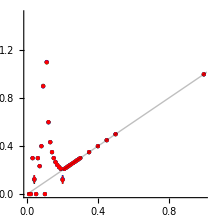

```mathematica
grTsfr=
Show[
ErrorListPlot[
{Transpose[
{translationSpeeds1[[All,{1,2}]],(ErrorBar /@ translationSpeeds[[All, 3]])}
],
Transpose[
{translationSpeeds2[[All,{1,2}]],(ErrorBar /@ translationSpeeds[[All, 3]])}
],
Transpose[
{translationSpeeds3[[All,{1,2}]],(ErrorBar /@ translationSpeeds[[All, 3]])}
],
Transpose[
{translationSpeeds4[[All,{1,2}]],(ErrorBar /@ translationSpeeds[[All, 3]])}
]}

,PlotRange->{{0,1},{0,1.5}},PlotStyle->{Black, Green,Blue, Red},LabelStyle->(FontFamily->"Helvetica"),AspectRatio->1,ImageSize->72*3],
Plot[x,{x,0,2.5},PlotStyle->Directive[Thick,Opacity[0.25,Black]]]
]
```

```mathematica
Export["translationSpeedsFR.pdf",grTsfr]
```

translationSpeedsFR.pdf

## Translation Angle

```mathematica
analyzeTranslationAngle[detDiameterPer2Pi_,framesPerDetDiameter_, angle_, noisePercent_]:=
Module[{tempdata, tempflow,tempangles},
JavaBlock[
tempdata=NNMDataNew[cd<>"\\testfiles\\translation_"<>ToString[detDiameterPer2Pi]<>"_"<>ToString[framesPerDetDiameter]<>"_"<>ToString[angle]<>"_"<>ToString[noisePercent]<>".da"];
tempflow={};
Do[
tempflow=Join[tempflow,NNMFlowNew[tempdata,RandomInteger[{100,300}],FlowRing->3][[1]]],
{100}];
tempflow=DeleteCases[tempflow, x_/;(x==Null || x[[5]]==0.)];
tempangles= ArcTan[#[[1]], #[[2]]]& /@ tempflow;
{Mean[tempangles], StandardDeviation[tempangles]}
]]
```

```mathematica
translationAngles=Join[{#},analyzeTranslationAngle[10,3,#,0]]& /@ Range[0,90, 3]
```

{{0,0.0000770649,0.00272705},{3,0.0584771,0.000284882},{6,0.0913044,0.00102789},{9,0.189428,0.00044915},{12,0.190652,0.000357316},{15,0.264581,0.000709565},{18,0.320497,0.000399908},{21,0.359676,0.00074954},{24,0.436516,0.000941107},{27,0.488659,0.00439537},{30,0.523868,0.000629394},{33,0.558958,0.00435105},{36,0.610247,0.000819226},{39,0.687886,0.000731037},{42,0.726086,0.000422409},{45,0.783619,0.000751159},{48,0.857042,0.000344894},{51,0.857039,0.000430068},{54,0.955525,0.0010524},{57,0.989033,0.000275933},{60,1.04634,0.00126866},{63,1.10617,0.000266846},{66,1.13814,0.0011443},{69,1.23638,0.000442871},{72,1.23769,0.00045205},{75,1.31049,0.000617799},{78,1.36882,0.000321237},{81,1.40664,0.000760392},{84,1.4833,0.000899967},{87,1.53542,0.00435718},{90,1.5708,0.00031716}}

```mathematica
translationAngles={#[[1]],#[[2]]*180/Pi,#[[3]]*180/Pi}& /@translationAngles
```

{{0,0.00441549,0.156249},{3,3.35049,0.0163225},{6,5.23136,0.0588939},{9,10.8534,0.0257344},{12,10.9236,0.0204727},{15,15.1594,0.0406551},{18,18.3631,0.022913},{21,20.6079,0.0429455},{24,25.0105,0.0539214},{27,27.9981,0.251836},{30,30.0154,0.0360616},{33,32.026,0.249297},{36,34.9646,0.0469382},{39,39.4129,0.0418854},{42,41.6016,0.0242023},{45,44.8981,0.0430382},{48,49.1049,0.019761},{51,49.1047,0.0246411},{54,54.7475,0.0602979},{57,56.6674,0.0158098},{60,59.9507,0.072689},{63,63.379,0.0152891},{66,65.2104,0.0655634},{69,70.8396,0.0253746},{72,70.9144,0.0259005},{75,75.0856,0.0353973},{78,78.4279,0.0184055},{81,80.5948,0.0435672},{84,84.987,0.0515643},{87,87.9728,0.249648},{90,90.,0.0181719}}

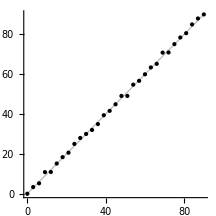

```mathematica
grTA=
Show[
ErrorListPlot[
Transpose[
{translationAngles[[All,{1,2}]],(ErrorBar /@ translationAngles[[All, 3]])}
],PlotStyle->Black,LabelStyle->(FontFamily->"Helvetica"),AspectRatio->1,ImageSize->72*3],
Plot[x,{x,0,90},PlotStyle->Directive[Thick,Opacity[0.25,Black]]]
]
```

```mathematica
Export["translationAngles.pdf",grTA]
```

translationAngles.pdf

## Translation Noise (w/ + w/o Filters)

```mathematica
analyzeTranslationNoise[detDiameterPer2Pi_,framesPerDetDiameter_, angle_, noisePercent_]:=
Module[{tempdata, tempflow,tempspeeds,tempangles},
JavaBlock[
tempdata=NNMDataNew[cd<>"\\testfiles\\translation_"<>ToString[detDiameterPer2Pi]<>"_"<>ToString[framesPerDetDiameter]<>"_"<>ToString[angle]<>"_"<>ToString[noisePercent]<>".da"];
tempflow={};
Do[
tempflow=Join[tempflow,NNMFlowNew[tempdata,RandomInteger[{100,300}],FlowRing->3][[1]]],
{100}];
tempflow=DeleteCases[tempflow, x_/;(x==Null || x[[5]]==0.)];
tempspeeds= Norm[{#[[1]], #[[2]]}]& /@ tempflow;
tempangles= ArcTan[#[[1]], #[[2]]]& /@ tempflow;
{Mean[tempspeeds], StandardDeviation[tempspeeds],Mean[tempangles], StandardDeviation[tempangles]}
]]
```

```mathematica
translationNoise=Join[{#},analyzeTranslationNoise[10,3, 60,#]]& /@ Range[0,50, 2]
```

{{0,2.8827,0.025073,1.04637,0.00130507},{2,3.00455,0.0362926,1.04481,0.0129563},{4,3.00511,0.0538169,1.04713,0.0140039},{6,3.00836,0.0662618,1.046,0.0138938},{8,3.00236,0.0704819,1.04472,0.0137679},{10,3.00333,0.0771205,1.04593,0.0149197},{12,3.00366,0.0883098,1.04603,0.0152509},{14,3.00564,0.0957216,1.04638,0.0166764},{16,2.99871,0.0935778,1.04875,0.0169538},{18,2.99514,0.102838,1.0469,0.0192139},{20,3.00067,0.106763,1.04649,0.0212804},{22,3.00089,0.106344,1.0464,0.0227172},{24,3.00497,0.121292,1.04573,0.0245958},{26,3.01417,0.118899,1.04609,0.0260343},{28,3.00054,0.119832,1.04521,0.029021},{30,3.00202,0.127016,1.04585,0.0294659},{32,3.00653,0.142212,1.04565,0.0320899},{34,3.00335,0.131262,1.04739,0.0351373},{36,2.98619,0.133972,1.04499,0.0359549},{38,3.01619,0.139191,1.042,0.0374423},{40,3.01121,0.155897,1.04453,0.037121},{42,2.99933,0.155283,1.05176,0.0412228},{44,3.00756,0.158885,1.04572,0.0423051},{46,3.0018,0.162056,1.05082,0.0434384},{48,3.02143,0.164211,1.04222,0.0463437},{50,3.01338,0.173875,1.04989,0.051083}}

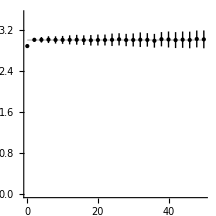

```mathematica
grTNs=
Show[
ErrorListPlot[
Transpose[
{translationNoise[[All,{1,2}]],(ErrorBar /@ translationNoise[[All, 3]])}
],PlotRange->{0,3.5},PlotStyle->Black,LabelStyle->(FontFamily->"Helvetica"),AspectRatio->1,ImageSize->72*3],
Plot[3.0,{x,0,50},PlotStyle->Directive[Thick,Opacity[0.25,Black]]]
]
```

```mathematica
Export["translationNoiseSpeeds.pdf",grTNs]
```

translationNoiseSpeeds.pdf

## Translation Noise and Fast Wave Aliasing

```mathematica
analyzeTranslation[detDiameterPer2Pi_,framesPerDetDiameter_, angle_, noisePercent_]:=
Module[{tempdata, tempflow,tempspeeds},
JavaBlock[
tempdata=NNMDataNew[cd<>"\\testfiles\\translation_"<>ToString[detDiameterPer2Pi]<>"_"<>ToString[framesPerDetDiameter]<>"_"<>ToString[angle]<>"_"<>ToString[noisePercent]<>".da"];
tempflow=NNMFlowNew[tempdata,RandomInteger[{100,300}]][[1]];
tempflow=Join[tempflow,NNMFlowNew[tempdata,RandomInteger[{100,300}]][[1]]];
tempflow=Join[tempflow,NNMFlowNew[tempdata,RandomInteger[{100,300}]][[1]]];
tempflow=Join[tempflow,NNMFlowNew[tempdata,RandomInteger[{100,300}]][[1]]];
tempflow=Join[tempflow,NNMFlowNew[tempdata,RandomInteger[{100,300}]][[1]]];
tempflow=DeleteCases[tempflow, x_/;x[[5]]==0.];
tempspeeds= Norm[{#[[1]], #[[2]]}]& /@ tempflow;
{Mean[tempspeeds], StandardDeviation[tempspeeds]}
]]
```

```mathematica
translationSpeeds0Noise=Join[{#},analyzeTranslation[10,#,60,0]]& /@ 
 Join[Range[0.01, 0.3, 0.01],Range[0.35, 0.45, 0.05],Range[0.5,2.5,0.5]]
```

{{0.01,0.,0.},{0.02,0.,0.},{0.03,0.300152,0.000263084},{0.04,0.121059,0.0335728},{0.05,0.,0.},{0.06,0.299856,0.000188498},{0.07,0.23312,0.000285567},{0.08,0.4,4.15491×10^-6},{0.09,0.899573,0.000556438},{0.1,0.,0.},{0.11,1.09955,0.000824709},{0.12,0.599698,0.0010794},{0.13,0.433276,0.000101364},{0.14,0.350002,0.0000535323},{0.15,0.299969,0.0000914562},{0.16,0.266667,3.73806×10^-6},{0.17,0.242889,0.0001462},{0.18,0.224969,0.0000714847},{0.19,0.211134,0.000283196},{0.2,0.119834,0.0331397},{0.21,0.210005,0.0000407747},{0.22,0.21999,0.000145699},{0.23,0.229886,0.000243039},{0.24,0.240063,0.000204166},{0.25,0.250048,0.0001532},{0.26,0.260045,0.00014643},{0.27,0.270033,0.0000649228},{0.28,0.280102,0.000160428},{0.29,0.28985,0.000228761},{0.3,0.299986,0.000104084},{0.35,0.350007,0.0000552361},{0.4,0.4,4.15491×10^-6},{0.45,0.450038,0.000200538},{0.5,0.499899,0.000146372},{1.,0.999862,0.000708874},{1.5,1.50009,0.000487201},{2.,1.99834,0.00336002},{2.5,2.50212,0.00534288}}

```mathematica
translationSpeeds5Noise=Join[{#},analyzeTranslation[10,#,60,5]]& /@ 
 Join[Range[0.01, 0.3, 0.01],Range[0.35, 0.45, 0.05],Range[0.5,2.5,0.5]]
```

{{0.01,3.94163,4.53147},{0.02,3.47086,2.96729},{0.03,0.30018,0.00204037},{0.04,0.121013,0.19801},{0.05,3.65827,3.30184},{0.06,0.299961,0.00197748},{0.07,0.233471,0.00179653},{0.08,0.399537,0.00281424},{0.09,0.902632,0.0133768},{0.1,3.80049,3.77526},{0.11,1.10246,0.0183031},{0.12,0.600286,0.00538116},{0.13,0.433428,0.00313728},{0.14,0.35015,0.00231064},{0.15,0.299969,0.00187781},{0.16,0.26684,0.00174134},{0.17,0.243053,0.00164459},{0.18,0.22486,0.00151776},{0.19,0.211095,0.00142379},{0.2,0.121742,0.189594},{0.21,0.210028,0.00153678},{0.22,0.220121,0.00165854},{0.23,0.230139,0.00167614},{0.24,0.23974,0.00183372},{0.25,0.250028,0.00181393},{0.26,0.260107,0.0018973},{0.27,0.270133,0.00190667},{0.28,0.280127,0.002012},{0.29,0.290115,0.00198994},{0.3,0.299985,0.00211108},{0.35,0.350243,0.0024011},{0.4,0.399385,0.00276856},{0.45,0.450302,0.00337815},{0.5,0.498716,0.00445148},{1.,0.994618,0.017844},{1.5,1.49337,0.0392351},{2.,1.95276,0.0617319},{2.5,2.45871,0.107188}}

```mathematica
translationSpeeds10Noise=Join[{#},analyzeTranslation[10,#,60,10]]& /@ 
 Join[Range[0.01, 0.3, 0.01],Range[0.35, 0.45, 0.05],Range[0.5,2.5,0.5]]
```

{{0.01,1.91371,1.68072},{0.02,2.09986,2.57224},{0.03,0.300157,0.00443991},{0.04,0.115419,0.105661},{0.05,1.9316,2.18301},{0.06,0.300323,0.00380446},{0.07,0.23351,0.00329258},{0.08,0.398987,0.00579635},{0.09,0.903329,0.0267778},{0.1,2.03456,3.24326},{0.11,1.10013,0.0374435},{0.12,0.60112,0.0107255},{0.13,0.433845,0.00619299},{0.14,0.350974,0.00474198},{0.15,0.300216,0.00396882},{0.16,0.266645,0.00357208},{0.17,0.242578,0.00315834},{0.18,0.225167,0.0028519},{0.19,0.204514,0.0167789},{0.2,0.11134,0.0700043},{0.21,0.200228,0.0204086},{0.22,0.220218,0.00339153},{0.23,0.230259,0.00332109},{0.24,0.240445,0.00340099},{0.25,0.250268,0.00358009},{0.26,0.260202,0.00361159},{0.27,0.27014,0.00396762},{0.28,0.280226,0.00406786},{0.29,0.290629,0.00403824},{0.3,0.300053,0.00438929},{0.35,0.35036,0.00473632},{0.4,0.399867,0.00553785},{0.45,0.44988,0.0070915},{0.5,0.498242,0.00905724},{1.,0.994488,0.0373277},{1.5,1.48594,0.0799498},{2.,1.93363,0.129002},{2.5,2.4362,0.307061}}

```mathematica
translationSpeeds15Noise=Join[{#},analyzeTranslation[10,#,60,15]]& /@ 
 Join[Range[0.01, 0.3, 0.01],Range[0.35, 0.45, 0.05],Range[0.5,2.5,0.5]]
```

{{0.01,1.45161,1.40973},{0.02,1.37467,1.87912},{0.03,0.300029,0.00601187},{0.04,0.103902,0.0669022},{0.05,1.4749,1.47554},{0.06,0.299932,0.00567722},{0.07,0.234006,0.00491591},{0.08,0.399713,0.00872788},{0.09,0.896597,0.0404432},{0.1,1.4065,1.71318},{0.11,1.09642,0.0548083},{0.12,0.600087,0.0162494},{0.13,0.433854,0.00947606},{0.14,0.351007,0.00701984},{0.15,0.300452,0.00583235},{0.16,0.26674,0.00503781},{0.17,0.242985,0.00483037},{0.18,0.224579,0.00654876},{0.19,0.176445,0.0404787},{0.2,0.117581,0.109087},{0.21,0.162306,0.042127},{0.22,0.218465,0.0102562},{0.23,0.230578,0.00498064},{0.24,0.239888,0.00518008},{0.25,0.250196,0.00539285},{0.26,0.260424,0.00544472},{0.27,0.270496,0.00590284},{0.28,0.280038,0.00626576},{0.29,0.29059,0.00609449},{0.3,0.300804,0.0062294},{0.35,0.35065,0.00689149},{0.4,0.399462,0.00850121},{0.45,0.448011,0.0107696},{0.5,0.498623,0.0136339},{1.,0.994201,0.0553168},{1.5,1.49143,0.133666},{2.,1.95561,0.228522},{2.5,2.48342,0.649584}}

```mathematica
translationSpeeds20Noise=Join[{#},analyzeTranslation[10,#,60,20]]& /@ 
 Join[Range[0.01, 0.3, 0.01],Range[0.35, 0.45, 0.05],Range[0.5,2.5,0.5]]
```

{{0.01,1.09088,0.893436},{0.02,1.18711,1.16687},{0.03,0.300842,0.00803903},{0.04,0.104491,0.0676327},{0.05,1.18427,1.51829},{0.06,0.301075,0.00756236},{0.07,0.233894,0.00899007},{0.08,0.398977,0.0110915},{0.09,0.899149,0.0578866},{0.1,1.093,0.793873},{0.11,1.09667,0.0792836},{0.12,0.601684,0.0212169},{0.13,0.432939,0.012178},{0.14,0.352204,0.00983262},{0.15,0.301584,0.0084155},{0.16,0.267132,0.00712929},{0.17,0.242565,0.00594651},{0.18,0.220184,0.0154141},{0.19,0.148924,0.0474484},{0.2,0.107609,0.0740015},{0.21,0.142863,0.048599},{0.22,0.208056,0.0229387},{0.23,0.230285,0.00829086},{0.24,0.241122,0.00716252},{0.25,0.250751,0.00689209},{0.26,0.261199,0.00771393},{0.27,0.270657,0.00761733},{0.28,0.281184,0.00781451},{0.29,0.290958,0.00863378},{0.3,0.301412,0.00876647},{0.35,0.351375,0.0099657},{0.4,0.398454,0.011452},{0.45,0.447597,0.0142073},{0.5,0.498385,0.0185267},{1.,1.0039,0.0798687},{1.5,1.49075,0.188023},{2.,1.9684,0.457556},{2.5,2.36574,0.553467}}

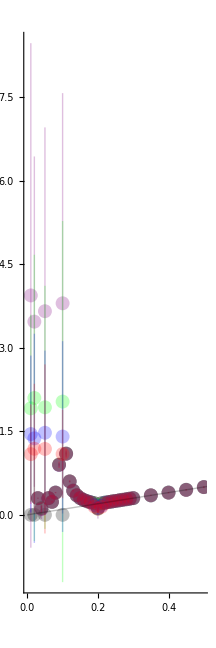

```mathematica
grTsNA=
Show[
ErrorListPlot[
{Transpose[
{translationSpeeds0Noise[[All,{1,2}]],(ErrorBar /@ translationSpeeds0Noise[[All, 3]])}
],
Transpose[
{translationSpeeds5Noise[[All,{1,2}]],(ErrorBar /@ translationSpeeds5Noise[[All, 3]])}
],
Transpose[
{translationSpeeds10Noise[[All,{1,2}]],(ErrorBar /@ translationSpeeds10Noise[[All, 3]])}
],
Transpose[
{translationSpeeds15Noise[[All,{1,2}]],(ErrorBar /@ translationSpeeds15Noise[[All, 3]])}
],
Transpose[
{translationSpeeds20Noise[[All,{1,2}]],(ErrorBar /@ translationSpeeds20Noise[[All, 3]])}
]},PlotRange->{{0,0.5},All},
PlotStyle->(Directive[#,AbsolutePointSize[10]]& /@{Opacity[0.25,Black],Opacity[0.25,Purple],Opacity[0.25,Green],Opacity[0.25,Blue], Opacity[0.25,Red]}),LabelStyle->(FontFamily->"Helvetica"),AspectRatio->3,ImageSize->72*3],
Plot[x,{x,0,2.5},PlotStyle->Directive[Thick,Opacity[0.25,Black]]]
]
```

```mathematica
Export["translationNoiseAndAliasing.pdf",grTsNA]
```

translationNoiseAmplitudes.pdf

## Serialize Source Speed

```mathematica
cd=SetDirectory[NotebookDirectory[]]
```

V:\Documents\k.vsd\_figures\vsdMeth\flow field

```mathematica
Save["sourceSpeedResults.m",{sourceSpeeds}]
```

## Source Speed

```mathematica
analyzeSource[detDiameterPer2Pi_,framesPerDetDiameter_, noisePercent_]:=
Module[{tempdata,tempflowObj, tempflow,tempspeeds},
JavaBlock[
tempdata=cd<>"\\testfiles\\source_"<>ToString[detDiameterPer2Pi]<>"_"<>ToString[framesPerDetDiameter]<>"_"<>ToString[noisePercent]<>".da";
Print[tempdata];
tempdata=NNMDataNew[tempdata];
tempflowObj=JavaNew[$NNJFlowClassPath,tempdata[[1]]];
tempflowObj@setFlowRing[3];
tempflowObj@setMaxShift[50];
tempflowObj@setCorrelationWindowLength[60];
tempflow=(tempflowObj@getResults[#,123-1])& /@ Range[100,300];
tempflow=DeleteCases[tempflow, x_/;x[[5]]<=0.75];
tempspeeds=#[[3]]&(* Norm[{#[[1]], #[[2]]}]&*) /@ tempflow;
{Mean[tempspeeds], StandardDeviation[tempspeeds]}
]]
```

```mathematica
sourceSpeeds=Join[{#},analyzeSource[10,#,0]]&  /@
 Join[Range[0.5,10,0.5]]
```

V:\Documents\k.vsd\_figures\vsdMeth\flow field\testfiles\source_10_0.5_0.da

V:\Documents\k.vsd\_figures\vsdMeth\flow field\testfiles\source_10_1._0.da

V:\Documents\k.vsd\_figures\vsdMeth\flow field\testfiles\source_10_1.5_0.da

V:\Documents\k.vsd\_figures\vsdMeth\flow field\testfiles\source_10_2._0.da

V:\Documents\k.vsd\_figures\vsdMeth\flow field\testfiles\source_10_2.5_0.da

V:\Documents\k.vsd\_figures\vsdMeth\flow field\testfiles\source_10_3._0.da

V:\Documents\k.vsd\_figures\vsdMeth\flow field\testfiles\source_10_3.5_0.da

V:\Documents\k.vsd\_figures\vsdMeth\flow field\testfiles\source_10_4._0.da

V:\Documents\k.vsd\_figures\vsdMeth\flow field\testfiles\source_10_4.5_0.da

V:\Documents\k.vsd\_figures\vsdMeth\flow field\testfiles\source_10_5._0.da

V:\Documents\k.vsd\_figures\vsdMeth\flow field\testfiles\source_10_5.5_0.da

V:\Documents\k.vsd\_figures\vsdMeth\flow field\testfiles\source_10_6._0.da

V:\Documents\k.vsd\_figures\vsdMeth\flow field\testfiles\source_10_6.5_0.da

V:\Documents\k.vsd\_figures\vsdMeth\flow field\testfiles\source_10_7._0.da

V:\Documents\k.vsd\_figures\vsdMeth\flow field\testfiles\source_10_7.5_0.da

V:\Documents\k.vsd\_figures\vsdMeth\flow field\testfiles\source_10_8._0.da

V:\Documents\k.vsd\_figures\vsdMeth\flow field\testfiles\source_10_8.5_0.da

V:\Documents\k.vsd\_figures\vsdMeth\flow field\testfiles\source_10_9._0.da

V:\Documents\k.vsd\_figures\vsdMeth\flow field\testfiles\source_10_9.5_0.da

V:\Documents\k.vsd\_figures\vsdMeth\flow field\testfiles\source_10_10._0.da

{{0.5,0.498974,0.0321497},{1.,1.07458,0.029606},{1.5,1.57099,0.000252504},{2.,1.93317,0.0000429844},{2.5,2.65267,0.0072918},{3.,3.01443,5.38943×10^-7},{3.5,3.50264,0.00990902},{4.,4.08672,0.038775},{4.5,4.58336,0.0116819},{5.,4.94739,5.42145×10^-6},{5.5,5.66308,0.0143875},{6.,6.02887,1.89407×10^-6},{6.5,6.51155,0.0170875},{7.,7.07111,0.0730238},{7.5,7.59255,0.017557},{8.,7.96181,1.34757×10^-6},{8.5,8.47558,0.0665547},{9.,9.0433,3.50295×10^-6},{9.5,9.52172,0.019821},{10.,9.8948,0.000022692}}

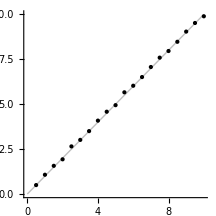

```mathematica
grSs=
Show[
ErrorListPlot[
Transpose[
{sourceSpeeds[[All,{1,2}]],(ErrorBar /@ sourceSpeeds[[All, 3]])}
],PlotRange->{{0,10},All},PlotStyle->Black,LabelStyle->(FontFamily->"Helvetica"),AspectRatio->1,ImageSize->72*3],
Plot[x,{x,0,10.},PlotStyle->Directive[Thick,Opacity[0.25,Black]]]
]
```

```mathematica
Export["sourceSpeeds.pdf",grSs]
```

sourceSpeeds.pdf

## Rotation Speed

```mathematica
analyzeRotation[rotationsPer2Pi_,framesPer2Pi_, noisePercent_]:=
Module[{tempdata,tempflowObj, tempflow,tempspeeds},
JavaBlock[
tempdata=NNMDataNew[cd<>"\\testfiles\\rotation_"<>ToString[rotationsPer2Pi]<>"_"<>ToString[framesPer2Pi]<>"_"<>ToString[noisePercent]<>".da"];
tempflowObj=JavaNew[$NNJFlowClassPath,tempdata[[1]]];
tempflowObj@setFlowRing[3];
tempflowObj@setMaxShift[15];
tempflowObj@setCorrelationWindowLength[30];
tempflow=(tempflowObj@getResults[#,123-1])& /@ Range[200,800];
tempflow=DeleteCases[tempflow, x_/;x[[5]]<=0.75];
tempspeeds=#[[4]]&(* Norm[{#[[1]], #[[2]]}]&*) /@ tempflow;
If[Length[tempspeeds]>1,
{Mean[tempspeeds], StandardDeviation[tempspeeds]},
{}]
]]
```

```mathematica
rotationSpeeds=Join[{#},analyzeRotation[1,#,10]]&  /@
 Join[Range[5, 60, 2]]
```

{{5},{7},{9},{11},{13},{15},{17},{19,-2.86479,9.06493×10^-16},{21,-3.33493,0.0582243},{23,-3.81972,4.44089×10^-16},{25},{27},{29},{31},{33},{35},{37},{39},{41},{43},{45,-7.267,0.000813034},{47,-7.58917,0.047332},{49,-7.73438,0.0792441},{51,-8.1318,0.103674},{53,-8.46712,0.0794408},{55,-8.72033,0.093967},{57,-9.07905,0.100209},{59,-9.42236,0.0941815}}

```mathematica
rotationSpeeds=
```

StandardDeviation::shlen: The argument {} should have at least two elements.

General::stop: Further output of StandardDeviation :: shlen will be suppressed during this calculation.

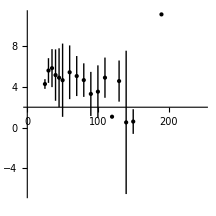

```mathematica
grRs=
Show[
ErrorListPlot[
Transpose[
{rotationSpeeds[[All,{1,2}]],(ErrorBar /@ rotationSpeeds[[All, 3]])}
],PlotRange->{{0,250},All},PlotStyle->Black,LabelStyle->(FontFamily->"Helvetica"),AspectRatio->1,ImageSize->72*3](*,
Plot[x,{x,0,5.},PlotStyle->Directive[Thick,Opacity[0.25,Black]]]*)
]
```

```mathematica
Export["rotationSpeeds.pdf",grSs]
```

sourceSpeeds.pdf